### Explicit Examples

```mathematica
α = ({{α1}, {α2}, {α3}, {α4}});
β1=({{β11}, {β12}, {β13}, {β14}});
β2=({{β21}, {β22}, {β23}, {β24}});
β3=({{β31}, {β32}, {β33}, {β34}});
β4=({{β41}, {β42}, {β43}, {β44}});
A0=({{0, 0, 0, 0}, {A021, 0, 0, 0}, {A031, A032, 0, 0}, {A041, A042, A043, 0}}); (* A0=({{A011, A012, A013, A014}, {A021, A022, A023, A024}, {A031, A032, A033, A034}, {A041, A042, A043, A044}}); *)
A1=({{0, 0, 0, 0}, {A121, 0, 0, 0}, {A131, A132, 0, 0}, {A141, A142, A143, 0}}); (* Subscript[A, 1]=({{A111, A112, A113, A114}, {A121, A122, A123, A124}, {A131, A132, A113, A134}, {A141, A142, A143, A144}}); *)
B0=({{0, 0, 0, 0}, {B021, 0, 0, 0}, {B031, B032, 0, 0}, {B041, B042, B043, 0}}); (* Subscript[B, 0]=({{B011, B012, B013, B014}, {B021, B022, B023, B024}, {B031, B032, B033, B034}, {B041, B042, B043, B044}}); *)
B1=({{0, 0, 0, 0}, {B121, 0, 0, 0}, {B131, B132, 0, 0}, {B141, B142, B143, 0}}); (* Subscript[B, 1]=({{B111, B112, B113, B114}, {B121, B122, B123, B124}, {B131, B132, B133, B134}, {B141, B142, B143, B144}}); *)
e = ({{1}, {1}, {1}, {1}});
higherConstraints[A011_,A012_,A013_,A014_,A021_,A022_,A023_,A024_,A031_,A032_,A033_,A034_,A041_,A042_,A043_,A044_,
A111_,A112_,A113_,A114_,A121_,A122_,A123_,A124_,A131_,A132_,A133_,A134_,A141_,A142_,A143_,A144_,
B011_,B012_,B013_,B014_,B021_,B022_,B023_,B024_,B031_,B032_,B033_,B034_,B041_,B042_,B043_,B044_,
B111_,B112_,B113_,B114_,B121_,B122_,B123_,B124_,B131_,B132_,B133_,B134_,B141_,B142_,B143_,B144_,
α1_,α2_,α3_,α4_,β11_,β12_,β13_,β14_,β21_,β22_,β23_,β24_,β31_,β32_,β33_,β34_,β41_,β42_,β43_,β44_] := {α1+α2+α3+α4==1,β11+β12+β13+β14==1,β21+β22+β23+β24==0,β31+β32+β33+β34==0,β41+β42+β43+β44==0,B121 β12+B131 β13+B132 β13+B141 β14+B142 β14+B143 β14==0,B121 β22+B131 β23+B132 β23+B141 β24+B142 β24+B143 β24==1,B121 β32+B131 β33+B132 β33+B141 β34+B142 β34+B143 β34==0,B121 β42+B131 β43+B132 β43+B141 β44+B142 β44+B143 β44==0,A021 α2+A031 α3+A032 α3+A041 α4+A042 α4+A043 α4==1/2,B021 α2+B031 α3+B032 α3+B041 α4+B042 α4+B043 α4==1,B021^2 α2+(B031+B032)^2 α3+(B041+B042+B043)^2 α4==3/2,A121 β12+A131 β13+A132 β13+A141 β14+A142 β14+A143 β14==1,A121 β22+A131 β23+A132 β23+A141 β24+A142 β24+A143 β24==0,A121 β32+A131 β33+A132 β33+A141 β34+A142 β34+A143 β34==-1,A121 β42+A131 β43+A132 β43+A141 β44+A142 β44+A143 β44==0,B121^2 β12+(B131+B132)^2 β13+(B141+B142+B143)^2 β14==1,B121^2 β22+(B131+B132)^2 β23+(B141+B142+B143)^2 β24==0,B121^2 β32+(B131+B132)^2 β33+(B141+B142+B143)^2 β34==-1,B121^2 β42+(B131+B132)^2 β43+(B141+B142+B143)^2 β44==2,B121 B132 β13+(B121 B142+(B131+B132) B143) β14==0,B121 B132 β23+(B121 B142+(B131+B132) B143) β24==0,B121 B132 β33+(B121 B142+(B131+B132) B143) β34==0,B121 B132 β43+(B121 B142+(B131+B132) B143) β44==1,1/2 (A132 B021 β13+(A142 B021+A143 (B031+B032)) β14)+1/3 (A132 B021 β33+(A142 B021+A143 (B031+B032)) β34)==0}
zmin = -14;
zmax = 1;
wmin = -3;
wmax = 3;
ymin = -4;
ymax = 4;
```

### SRI2W1

{True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}

7.72052

-Graphics3D-

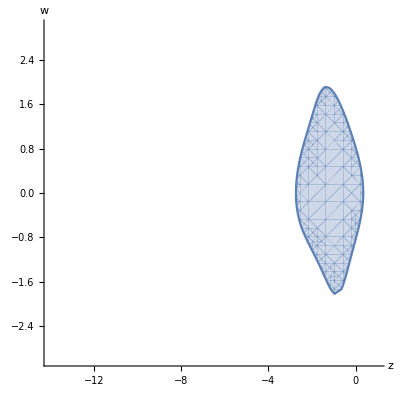

```mathematica
Clear[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
Get["stableRegionsEq.mx"]


higherConstraints[A011,A012,A013,A014,A021,A022,A023,A024,A031,A032,A033,A034,A041,A042,A043,A044,
A111,A112,A113,A114,A121,A122,A123,A124,A131,A132,A133,A134,A141,A142,A143,A144,
B011,B012,B013,B014,B021,B022,B023,B024,B031,B032,B033,B034,B041,B042,B043,B044,
B111,B112,B113,B114,B121,B122,B123,B124,B131,B132,B133,B134,B141,B142,B143,B144,
α1,α2,α3,α4,β11,β12,β13,β14,β21,β22,β23,β24,β31,β32,β33,β34,β41,β42,β43,β44]
stableRegions = Simplify[stableRegionsEq];
Re[NIntegrate[Boole[Abs[stableRegions]<1],{z,zmin,zmax},{w,wmin,wmax},Method->{"AdaptiveMonteCarlo"}]]
RegionPlot3D[Abs[stableRegions /. {z-> x + ⅈ y}]<1,{x,zmin,zmax},{y,ymin,ymax},{w,wmin,wmax},AxesLabel->Automatic]
RegionPlot[Abs[stableRegions]<1,{z,zmin,zmax},{w,wmin,wmax},AxesLabel->Automatic,Axes->True,Frame->None]
```

```mathematica
stableRegions = Simplify[stableRegionsEq];
Get["stableRegionsEq.mx"]
```

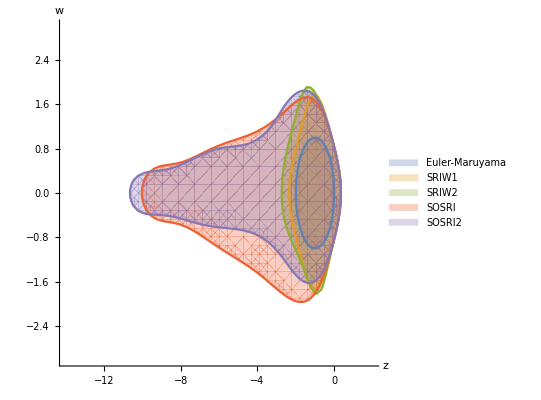

```mathematica
EMRegion = Abs[1+z]^2 + w^2;
SRIW1Region = stableRegions /. {A021-> 3/4,A031->0,A032-> 0,A041-> 0,A042-> 0,A043-> -0,A121 ->  1/4,A131->  1, A132-> 0,A141->  0, A142->0, A143->  1/4,B021-> 3/2, B031-> 0, B032->0, B041-> 0,B042->  0, B043-> 0, B121-> 1/2, B131-> -1,B132-> 0,B141-> -5,B142-> 3,B143-> 1/2,α1->1/3,α2-> 2/3,α3-> 0,α4-> 0,β11->-1,β12->4/3,β13-> 2/3,β14-> 0,β21-> -1,β22-> 4/3,β23-> -1/3,β24-> 0,β31-> 2,β32-> -4/3,β33-> -2/3,β34 -> 0,β41-> -2,β42-> 5/3,β43-> -2/3,β44 -> 1};
SRIW2Region = stableRegions /. {A021-> 1,A031->1/4,A032-> 1/4,A041-> 0,A042-> 0,A043-> 0,A121 ->  1/4,A131->  1, A132-> 0,A141->  0, A142->0, A143->  1/4,B021-> 0, B031->1, B032->1/2, B041-> 0,B042->  0, B043-> 0, B121-> -1/2, B131-> 1,B132-> 0,B141-> 2,B142-> -1,B143-> 1/2,α1->1/6,α2-> 1/6,α3->2/3,α4-> 0,β11->-1,β12->4/3,β13-> 2/3,β14-> 0,β21-> 1,β22-> -4/3,β23-> 1/3,β24-> 0,β31-> 2,β32-> -4/3,β33-> -2/3,β34 -> 0,β41-> -2,β42-> 5/3,β43-> -2/3,β44 -> 1};
SRIOpt1Region = stableRegions /.{A021-> -0.04199224421316468,A031-> 2.842612915017106,A032-> -2.0527723684000727,A041-> 4.338237071435815,A042-> -2.8895936137439793,A043-> 2.3017575594644466,A121-> 0.26204282091330466,A131-> 0.20903646383505375,A132-> -0.1502377115150361,A141-> 0.05836595312746999,A142-> 0.6149440396332373,A143-> 0.08535117634046772,B021-> -0.21641093549612528,B031-> 1.5336352863679572,B032-> 0.26066223492647056,B041-> -1.0536037558179159,B042-> 1.7015284721089472,B043-> -0.20725685784180017,B121-> -0.5119011827621657,B131-> 2.67767339866713,B132-> -4.9395031322250995,B141-> 0.15580956238299215,B142-> 3.2361551006624674,B143-> -1.4223118283355949,α1-> 1.140099274172029,α2-> -0.6401334255743456,α3-> 0.4736296532772559,α4-> 0.026404498125060714,β11-> -1.8453464565104432,β12-> 2.688764531100726,β13-> -0.2523866501071323,β14-> 0.40896857551684956,β21-> 0.4969658141589478,β22-> -0.5771202869753592,β23-> -0.12919702470322217,β24-> 0.2093514975196336,β31-> 2.8453464565104425,β32-> -2.688764531100725,β33-> 0.2523866501071322,β34-> -0.40896857551684945,β41-> 0.11522663875443433,β42-> -0.57877086147738,β43-> 0.2857851028163886,β44-> 0.17775911990655704};
SRIOpt2Region = stableRegions /. {A021-> 0.13804532298278663,A031->0.5818361298250374,A032->  0.4181638701749618,A041-> 0.4670018408674211,A042->  0.8046204792187386,A043->-0.27162232008616016,A121 ->  0.45605532163856893,A131->  0.7555807846451692, A132-> 0.24441921535482677,A141->  0.6981181143266059, A142->0.3453277086024727, A143->-0.04344582292908241,B021->0.08852381537667678, B031-> 1.0317752458971061, B032->0.4563552922077882, B041-> 1.73078280444124,B042->  -0.46089678470929774, B043-> -0.9637509618944188, B121-> 0.6753186815412179, B131-> -0.07452812525785148,B132-> -0.49783736486149366,B141->-0.5591906709928903,B142-> 0.022696571806569924,B143->-0.8984927888368557,α1-> -0.15036858140642623,α2-> 0.7545275856696072,α3-> 0.686995463807979,α4-> -0.2911544680711602,β11-> -0.45315689727309133,β12->0.8330937231303951,β13-> 0.3792843195533544,β14-> 0.24077885458934192,β21-> -0.4994383733810986,β22-> 0.9181786186154077,β23-> -0.25613778661003145,β24->-0.16260245862427797,β31-> 1.4531568972730915,β32-> -0.8330937231303933,β33-> -0.3792843195533583,β34 ->-0.24077885458934023,β41-> -0.4976090683622265,β42-> 0.9148155835648892,β43-> -1.4102107084476505,β44 -> 0.9930041932449877};
SetOptions[RegionPlot,BaseStyle->{FontFamily->"Ariel",FontSize->22}];
RegionPlot[{Abs[EMRegion]<1,Abs[SRIW1Region]<1,Abs[SRIW2Region]<1,Abs[SRIOpt1Region]<1,Abs[SRIOpt2Region]<1},{z,zmin,2},{w,-3,3},AxesLabel->Automatic,Axes->True,Frame->None,PlotLegends->{Style[Euler-Maruyama,22],Style[SRIW1,22],Style[SRIW2,22],Style[SOSRI,22],Style[SOSRI2,22]}]
```

```mathematica
Export["DiagonalStability.pdf",%]
```

DiagonalStability.pdf

```mathematica
Directory[]
```

D:\OneDrive\Computer\Documents